```mathematica
f[x_,y_] :=  (y^2-x +y/4+ x y + Log[x^2+y^4+1])Exp[-(x^2+y^2)];
```

The minimum is located in {0.530374, -0.253081}and it value is -0.292219

Execution time: 0.937234 seconds

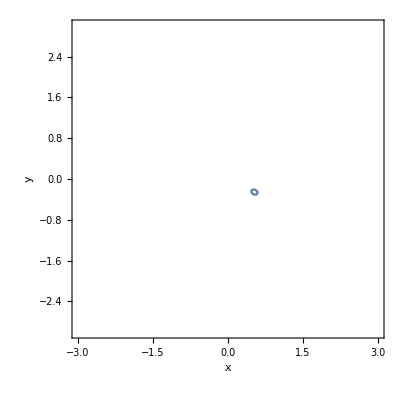

RandomPoint::creg: The first argument DiscretizeGraphics[Point[{}]] is expected to be a parameter-free region.

DiscretizeGraphics::rnimpl: The function DiscretizeGraphics is not implemented for Point[{}].

RandomPoint::creg: The first argument GraphicsBox[{GraphicsComplexBox[{{3., 0.201809}, {2.992479034202132, 0.206765}, {2.819921829471025, 0.1800781705289744}, {2.78571, 0.190313}, {2.7699, 0.1984737814337319}, {2.61676, 0.168951}, {2.57143, 0.179709}, {2.54678, 0.189639}, {2.41095, 0.160475}, {2.35714, 0.1705039299905844}, Skeleton[186]}, {{}, {}, TagBox[TooltipBox[{Directive[Skeleton[2]], LineBox[Skeleton[1]]},RowBox[{RowBox[{\"Times\", \"[\", RowBox[{\"«\", \"2\", \"»\"}], \"]\"}], \"==\", \"0\"}]],Annotation[#, Times[Skeleton[2]] == 0, \"Tooltip\"]& ]}], {}},Skeleton[12],AspectRatio->1,AxesLabel->{None, None},AxesOrigin->{0., 0.},DisplayFunction->Identity,FrameLabel->{{FormBox[RowBox[{\"«\", \"1\", \"»\"}], TraditionalForm], None}, {FormBox[RowBox[{\"«\", \"1\", \"»\"}], TraditionalForm], None}},FrameTicks->{{Automatic, Automatic}, {Automatic, Automatic}},GridLines->{None, None},ImageSize->{11., Automatic},Ticks->{Automatic, Automatic}] is expected to be a parameter-free region.

```mathematica
k = 0;
s = 1;
maxDiameter = 0.2;
maxDistance = 1;

{time, result} = Timing[
While[maxDistance > maxDiameter,
	contour = ContourPlot[f[x, y] == k, {x, -3, 3}, {y, -3, 3}];
	points = Cases[Normal@contour, Line[x_] :> x, 100];
	If[points == {},
		(*There's no point with that value in the function*)
		s = s / 2;
		k = k + s,
		(
		k = k - s;
		region = DiscretizeGraphics[Point@Flatten[points, 1]];
		points = RandomPoint[region, 100];
		maxDistance = Max[Table[Norm[p1 - p2], {p1, points}, {p2, points}]];
		)
	]
]
minimum = Mean[points];
];
message = StringJoin["The minimum is located in ", ToString[minimum], "and it value is ", ToString[f[minimum]]];
Print[message]
Print["Execution time: ", time, " seconds"];
Show[contour]
```